```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT]
```

```mathematica
leads=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/leads/l"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{{{-0.508689-0.228063 ⅈ,0.136148+0.284257 ⅈ,0.0853769-0.158561 ⅈ,-0.110588-0.00619769 ⅈ,0.0215379+0.0715145 ⅈ,0.0457869-0.0291003 ⅈ,-0.0325223-0.028399 ⅈ,-0.0145971+0.0304001 ⅈ,34,0.00274262+0.00219178 ⅈ,0.00105054-0.000325808 ⅈ,-0.00322045-0.00194508 ⅈ,0.000678236+0.00108729 ⅈ,0.0027963+0.00143539 ⅈ,-0.00215472-0.00162123 ⅈ,-0.00161361-0.00075783 ⅈ,0.00299987+0.00189417 ⅈ},48,{1}},499,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=leads[[Round[ω*100+251]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
(*IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]*)
```

```mathematica
(*IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]*)
```

```mathematica
(*gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]*)
```

```mathematica
(*grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]*)
```

```mathematica
(*Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]*)
```

```mathematica
(*GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]*)
```

```mathematica
(*tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]*)
```

```mathematica
(*pris=Compile[{ω},tr[ω,0.0001,5,0,100],CompilationTarget->"C",Parallelization->True]*)
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
unit[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Inverse[Module[{b=β[ω,δ,t,ϵ,50],F},(*F[ν_]:= {ν,ν};*)ReplacePart[b,(*Table[F[RandomSample[{RandomInteger[{1,14}]},1]]//Flatten,1]*){{n,n}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
leftside[ω_,ϵ1_,m_,x_]:= Module[{J=SL[ω,0.0001,1,0,m]},list={RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,1],50],Table[unit[ω,0.0001,1,0,0,1],50]]]};Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[T[1,m]].J.T[1,m]].list[[1,ζ]],{ζ,1,x}];
 J=J]
```

```mathematica
GN1N1[ω_,ϵ1_,m_,x_]:= Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T[1,m].leftside[ω,ϵ1,m,x].T[1,m]].SL[ω,0.0001,1,0,m]
```

```mathematica
support1[m_,n_]:=n*IdentityMatrix[m]
```

```mathematica
Gnonl[ω_,ϵ1_,m_]:= Module[{J=SL[ω,0.0001,1,0,m],A=T[1,m]},Do[J=J.A.leftside[ω,ϵ1,m,n],{n,1,100}];J=J].T[1,m].GN1N1[ω,ϵ1,m,100]
```

```mathematica
Gnonl[0,0,50]//AbsoluteTiming
```

{0.000061,SL[0,0.0001,1,0,50].T[1,50].leftside[0,0,50,1].T[1,50].leftside[0,0,50,2].T[1,50].leftside[0,0,50,3].T[1,50].leftside[0,0,50,4].T[1,50].leftside[0,0,50,5].T[1,50].leftside[0,0,50,6].T[1,50].leftside[0,0,50,7].T[1,50].leftside[0,0,50,8].T[1,50].leftside[0,0,50,9].T[1,50].leftside[0,0,50,10].T[1,50].GN1N1[0,0,50,10]}

```mathematica
Σ[ω_]:= T[1,50].SL[ω,0.0001,1,0,50].T[1,50]
```

```mathematica
Γ[ω_]:= ⅈ(Σ[ω]-ConjugateTranspose[Σ[ω]])
```

```mathematica
tr[ω_,ϵ1_]:=Tr[Γ[ω].Gnonl[ω,ϵ1,50].Γ[ω].ConjugateTranspose[Gnonl[ω,ϵ1,50]]]
```

```mathematica
tr[0.5,1]
```

-1.68145×10^8-1.03732×10^8 ⅈ

```mathematica
tr[1,0]
```

32.7087+3.95842×10^-16 ⅈ

```mathematica
Timing[Gnonl[0,0,50]]
```

{62.7574,{{0.49689+0. ⅈ,0.+0.419159 ⅈ,-0.000824038+0. ⅈ,0.+0.164335 ⅈ,-0.000310543+0. ⅈ,0.+0.103518 ⅈ,-0.0000683186+0. ⅈ,0.+0.0750303 ⅈ,0.0000748403+0. ⅈ,0.+0.0582946 ⅈ,0.000167971+0. ⅈ,0.+0.0472057 ⅈ,0.000230967+0. ⅈ,24,0.+0.00707278 ⅈ,0.000185413+0. ⅈ,0.+0.0058718 ⅈ,0.000156734+0. ⅈ,0.+0.00472992 ⅈ,0.000126821+0. ⅈ,0.+0.00363391 ⅈ,0.000095943+0. ⅈ,0.+0.0025721 ⅈ,0.0000643525+0. ⅈ,0.+0.00153399 ⅈ,0.0000322927+0. ⅈ,0.+0.000509799 ⅈ},48,{1}}}
 |  |  |  |

```mathematica
Clear[Gnonl]
```

```mathematica
device[ω_,δ_,t_,ϵ_,ϵ1_,m_,num1_,num2_,n1_,n2_]:=Module[{Tin=T[1,m],list,b2},
list={RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,n1],num1],Table[unit[ω,0.0001,1,0,ϵ1,n2],num2] ,Table[unit[ω,0.0001,1,0,0,1],50-num2-num1]]]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT[ω,δ,t,ϵ,50][[ζ,ζ]]]].ConjugateTranspose[Tin].J.Tin].Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT[ω,δ,t,ϵ,50][[ζ,ζ]]]],{ζ,1,50}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.Tin.SL[ω,0.0001,1,0,m].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].Tin.sl1.Tin].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]]
```

```mathematica
g66[ω_,ϵ1_,m_,x_]:= Inverse[IdentityMatrix[m]-LEFT[ω,0.0001,1,0,50].T[1,m].sl[ω,ϵ1,m,7].T[1,m]].LEFT[ω,0.0001,1,0,50]
```

```mathematica
gfinal33[ω_,ϵ1_,m_,x_]:= sl[ω,ϵ1,50,3].(IdentityMatrix[m]+T[1,m].sl[ω,ϵ1,50,4].(ConjugateTranspose[T[1,m]]+T[1,m].sl[ω,ϵ1,50,5].(ConjugateTranspose[T[1,m]]+T[1,m].g66[ω,ϵ1,50,5].ConjugateTranspose[T[1,m]].sl[ω,ϵ1,50,5].ConjugateTranspose[T[1,m]]).sl[ω,ϵ1,50,4].ConjugateTranspose[T[1,m]])).sl[ω,ϵ1,50,3]
```

```mathematica
Clear[gfinal33]
```

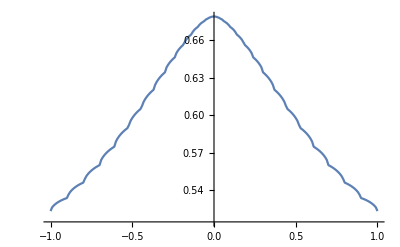

```mathematica
ListLinePlot[Table[{ω,-Im[sl[ω,0,50,3][[2,2]]]},{ω,Range[-1,1,0.01]}]]
```

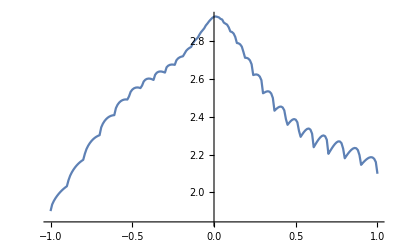

```mathematica
ListLinePlot[Table[{ω,-Im[gfinal33[ω,0,50][[2,2]]]},{ω,Range[-1,1,0.01]}]]
```

```mathematica
gfinal33[ω_,ϵ1_,m_]:=Module[{g33= sl[ω,ϵ1,m,3], g44=sl[ω,ϵ1,m,4], g55=sl[ω,ϵ1,m,5],g66f=sl[ω,ϵ1,m,6],T=T[1,m]},g33+g33.T.g44.T.g33+g33+g33.T.g44.T.g55.T.g44.T.g33+g33+g33.T.g44.T.g55.T.g66f.T.g55.T.g44.T.g33+g33+g33.T.g44.T.g55.T.g66f.T.sl[ω,ϵ1,m,7].T.g66f.T.g55.T.g44.T.g33+g33+g33.T.g44.T.g55.T.g66f.T.sl[ω,ϵ1,m,7].T.sl[ω,ϵ1,m,8].T.sl[ω,ϵ1,m,7].T.g66f.T.g55.T.g44.T.g33]
```

```mathematica
il5[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].sl[ω,0,m,5].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
ir5[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-sl[ω,0,m,5].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].sl[ω,0,m,5]
```

```mathematica
gdd5[ω_,δ_,t_,ϵ_,m_]:= il5[ω,δ,t,ϵ,m]-ConjugateTranspose[il5[ω,δ,t,ϵ,m]]
```

```mathematica
grr5[ω_,δ_,t_,ϵ_,m_]:= ir5[ω,δ,t,ϵ,m]-ConjugateTranspose[ir5[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal5[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].il5[ω,δ,t,ϵ,m]
```

```mathematica
GNON5[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal5[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal5[ω,δ,t,ϵ,m]]
```

```mathematica
tr5[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd5[ω,δ,t,ϵ,m].T[t,m].grr5[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON5[ω,δ,t,ϵ,m].T[t,m].GNON5[ω,δ,t,ϵ,m]]]
```

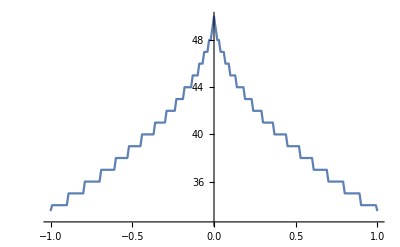

```mathematica
ListLinePlot[Table[{ω,tr5[ω,0.0001,1,0,50]},{ω,Range[-1,1,0.01]}]]
```

```mathematica
il3[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].gfinal33[ω,0,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
ir3[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-gfinal33[ω,0,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].gfinal33[ω,0,m]
```

```mathematica
gdd3[ω_,δ_,t_,ϵ_,m_]:= il3[ω,δ,t,ϵ,m]-ConjugateTranspose[il3[ω,δ,t,ϵ,m]]
```

```mathematica
grr3[ω_,δ_,t_,ϵ_,m_]:= ir3[ω,δ,t,ϵ,m]-ConjugateTranspose[ir3[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal3[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].il3[ω,δ,t,ϵ,m]
```

```mathematica
GNON3[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal3[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal3[ω,δ,t,ϵ,m]]
```

```mathematica
tr3[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd3[ω,δ,t,ϵ,m].T[t,m].grr3[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON3[ω,δ,t,ϵ,m].T[t,m].GNON3[ω,δ,t,ϵ,m]]]
```